```mathematica
datasetFile = "engine_gpr_dataset.xlsx"; (* full path if not in the working directory *)

nOracleTrain   = 600;  (* size of the reference "digital-twin" GPR (ground-truth stand-in) *)
nInitTrain     = 60;   (* size of the warm-start sample = already-tested points          *)
nCandidatesAcq = 1500; (* random-search pool size for maximizing the acquisition function *)
batchSize      = 4;    (* candidates proposed per iteration (batch synchrony)             *)
nIterations    = 8;    (* number of BO iterations                                          *)
t4Percentile   = 0.75; (* custom threshold: feasible region = T4 below this percentile     *)
randomSeed     = 2026;

SeedRandom[randomSeed];
```

```mathematica
(* ============================================================================
   1. LOAD THE DATA  (Import + Part indexing)
   ============================================================================ *)

motordata = Import["C:\\Users\\akrem\\Desktop\\work\\work\\motor opt\\engine_gpr_dataset.xlsx"][[1]];
(* motordata[[1]] is the header row. Column positions (1-indexed):
     1  Dataset            11 InjCrv_qPoI2
     2  APP_r              12 EnvT_t
     3  EGR_r              13 CEngDs_t
     4  InjCrv_qMI         14 BattU_u
     5  InjCrv_qSetUnBal   15 Epm_nEng
     6  ThrVlv_rAct        16 RailP_p
     7  InjCrv_phiPiI1     17 Torque_Nm
     8  InjCrv_phiMI1      18 T4_degC
     9  InjCrv_phiPoI2     19 NOx_ppm
     10 InjCrv_qPiI1
   In this workbook, rows 2..5001 are "DoE_Training" and rows 5002..6801 are
   "WHTC_Validation" (a contiguous block each - check yours with
   Union[motordata[[2 ;; -1, 1]]] and Position if you use a different file). *)

doeRows = motordata[[2 ;; 5001]];
Print["Loaded ", Length[doeRows], " DoE_Training rows."];

actuatorPos = {2, 3, 4, 5, 6, 7, 8, 9, 10, 11};  (* 10 calibratable actuator parameters *)
contextPos  = {12, 13, 14, 15, 16};              (* fixed operating-point variables     *)
torquePos = 17; t4Pos = 18; noxPos = 19;
```

Loaded 5000 DoE_Training rows.

```mathematica
XallDesign  = doeRows[[All, actuatorPos]];
XallContext = doeRows[[All, contextPos]];

lb = Min /@ Transpose[XallDesign];
ub = Max /@ Transpose[XallDesign];
contextFixed = Median /@ Transpose[XallContext];

Print["Fixed operating point (EnvT_t, CEngDs_t, BattU_u, Epm_nEng, RailP_p): ", contextFixed];
```

Fixed operating point (EnvT_t, CEngDs_t, BattU_u, Epm_nEng, RailP_p): {20.2717,82.5702,12.99,2439.72,1.18574×10^6}

```mathematica
oracleIdx = RandomSample[Range[Length[doeRows]], nOracleTrain];
oracleX   = doeRows[[oracleIdx, Join[actuatorPos, contextPos]]];

Print["Training oracle models on ", Length[oracleIdx], " points..."];
oracleTorque = Predict[oracleX -> doeRows[[oracleIdx, torquePos]],
   Method -> {"GaussianProcess", "CovarianceType" -> "SquaredExponential" + "RationalQuadratic"},
   PerformanceGoal -> "Quality"];
oracleT4 = Predict[oracleX -> doeRows[[oracleIdx, t4Pos]],
   Method -> {"GaussianProcess", "CovarianceType" -> "SquaredExponential" + "RationalQuadratic"},
   PerformanceGoal -> "Quality"];
oracleNOx = Predict[oracleX -> doeRows[[oracleIdx, noxPos]],
   Method -> {"GaussianProcess", "CovarianceType" -> "SquaredExponential" + "RationalQuadratic"},
   PerformanceGoal -> "Quality"];
Print["Oracle models ready."];

evaluateOracle[xFull_?(VectorQ[#, NumericQ] &)] := {oracleTorque[xFull], oracleT4[xFull], oracleNOx[xFull]};
```

Training oracle models on 600 points...

Oracle models ready.

```mathematica
initIdx = RandomSample[Complement[Range[Length[doeRows]], oracleIdx], nInitTrain];
Xtrain  = doeRows[[initIdx, actuatorPos]];
yTorque = doeRows[[initIdx, torquePos]];
yT4     = doeRows[[initIdx, t4Pos]];
yNOx    = doeRows[[initIdx, noxPos]];

Print["Warm-started the BO surrogate with ", Length[Xtrain], " already-tested points."];
```

Warm-started the BO surrogate with 60 already-tested points.

```mathematica
(* combined-kernel GP predictor: trained on design ++ fixed-context vectors *)
buildDesignGP[X_, y_] := Predict[(Join[#, contextFixed] & /@ X) -> y,
   Method -> {"GaussianProcess", "CovarianceType" -> "SquaredExponential" + "RationalQuadratic"},
   PerformanceGoal -> "Quality"];

meanOf[predictor_, xvec_?(VectorQ[#, NumericQ] &)] := Mean[predictor[xvec, "Distribution"]];
stdOf[predictor_, xvec_?(VectorQ[#, NumericQ] &)] := StandardDeviation[predictor[xvec, "Distribution"]];

(* closed-form Expected Improvement *)
expectedImprovement[mu_?NumericQ, sigma_?NumericQ, best_?NumericQ] :=
  If[sigma < 10^-8, 0.,
   With[{z = (mu - best)/sigma},
    sigma*(z*CDF[NormalDistribution[0, 1], z] + PDF[NormalDistribution[0, 1], z])]];

(* custom Pareto-front filter (no built-in multi-objective Pareto function in
   Wolfram Language): obj is a list of vectors, ALL objectives MAXIMIZED;
   returns indices of the non-dominated points *)
paretoIndices[obj_] := Module[{n = Length[obj], dominated},
   dominated = Table[
     AnyTrue[Delete[Range[n], i],
       (And @@ Thread[obj[[#]] >= obj[[i]]] &&
         Or @@ Thread[obj[[#]] > obj[[i]]]) &],
     {i, n}];
   Pick[Range[n], dominated, False]
];
```

```mathematica
t4Threshold = Quantile[yT4, t4Percentile];
Print["Custom threshold on T4: T4 <= ", NumberForm[t4Threshold, {5, 1}], " degC"];

iterationLog = {}; (* {iteration, bestFeasibleTorque, nFeasible} *)

Do[
  predTorque = buildDesignGP[Xtrain, yTorque];
  predNOx    = buildDesignGP[Xtrain, yNOx];
  predT4     = buildDesignGP[Xtrain, yT4];

  feasMask = Thread[yT4 <= t4Threshold];
  {minT, maxT} = MinMax[yTorque];
  {minN, maxN} = MinMax[yNOx];
  feasIdx = Flatten[Position[feasMask, True]];
  useIdx = If[Length[feasIdx] > 0, feasIdx, Range[Length[yTorque]]];

  (* shared candidate pool for this iteration; candidates are 10-D design
     vectors, so every GP query needs contextFixed appended first *)
  candidates = Table[RandomReal[{lb[[j]], ub[[j]]}], {nCandidatesAcq}, {j, Length[lb]}];
  candFull = Join[#, contextFixed] & /@ candidates;
  candMu1  = meanOf[predTorque, #] & /@ candFull;
  candS1   = stdOf[predTorque, #]  & /@ candFull;
  candMu2  = meanOf[predNOx, #]    & /@ candFull;
  candS2   = stdOf[predNOx, #]     & /@ candFull;
  candPF   = CDF[predT4[#, "Distribution"], t4Threshold] & /@ candFull;

  chosenIdx = {};
  newPts = Table[
    lambda1 = RandomReal[{0.05, 0.95}];
    lambda2 = 1 - lambda1;
    zBest = Max[lambda1*(yTorque[[useIdx]] - minT)/(maxT - minT) +
       lambda2*(maxN - yNOx[[useIdx]])/(maxN - minN)];
    acqVals = Table[
      If[MemberQ[chosenIdx, k], -1,
       Module[{muZ, sigZ, ei},
         muZ = lambda1*(candMu1[[k]] - minT)/(maxT - minT) +
            lambda2*(maxN - candMu2[[k]])/(maxN - minN);
         sigZ = Sqrt[(lambda1/(maxT - minT))^2*candS1[[k]]^2 +
             (lambda2/(maxN - minN))^2*candS2[[k]]^2];
         ei = expectedImprovement[muZ, sigZ, zBest];
         ei*candPF[[k]]
       ]],
      {k, nCandidatesAcq}];
    bestK = First[Ordering[acqVals, -1]];
    AppendTo[chosenIdx, bestK];
    candidates[[bestK]],
    {batchSize}
  ];

  newObs = evaluateOracle[Join[#, contextFixed]] & /@ newPts;
  Xtrain  = Join[Xtrain, newPts];
  yTorque = Join[yTorque, newObs[[All, 1]]];
  yT4     = Join[yT4,     newObs[[All, 2]]];
  yNOx    = Join[yNOx,    newObs[[All, 3]]];

  currentFeas = Flatten[Position[Thread[yT4 <= t4Threshold], True]];
  bestFeasTorque = If[Length[currentFeas] > 0, Max[yTorque[[currentFeas]]], Missing["None"]];
  AppendTo[iterationLog, {iter, bestFeasTorque, Length[currentFeas]}];
  Print["Iteration ", iter, "/", nIterations, " - archive: ", Length[Xtrain],
    " - feasible: ", Length[currentFeas], " - best feasible torque: ", bestFeasTorque],
  {iter, 1, nIterations}
];
```

Custom threshold on T4: T4 <= 208.0 degC

Iteration 1/8 - archive: 64 - feasible: 49 - best feasible torque: 131.159

Iteration 2/8 - archive: 68 - feasible: 52 - best feasible torque: 155.187

Iteration 3/8 - archive: 72 - feasible: 55 - best feasible torque: 155.187

Iteration 4/8 - archive: 76 - feasible: 58 - best feasible torque: 155.187

Iteration 5/8 - archive: 80 - feasible: 61 - best feasible torque: 155.187

Iteration 6/8 - archive: 84 - feasible: 64 - best feasible torque: 155.187

Iteration 7/8 - archive: 88 - feasible: 65 - best feasible torque: 155.187

Iteration 8/8 - archive: 92 - feasible: 67 - best feasible torque: 156.921

```mathematica
finalFeasIdx = Flatten[Position[Thread[yT4 <= t4Threshold], True]];

If[Length[finalFeasIdx] == 0,
  Print["WARNING: no feasible point satisfies the T4 threshold - consider \
raising t4Percentile or nIterations."],

  objMatrix = Transpose[{yTorque[[finalFeasIdx]], -yNOx[[finalFeasIdx]]}];
  paretoGlobalIdx = finalFeasIdx[[paretoIndices[objMatrix]]];

  paretoRows = SortBy[
    MapThread[Join[#1, {#2, #3, #4}] &,
      {Xtrain[[paretoGlobalIdx]], yTorque[[paretoGlobalIdx]],
       yT4[[paretoGlobalIdx]], yNOx[[paretoGlobalIdx]]}],
    -#[[11]] &]; (* sort by Torque, descending *)

  Print["\nPareto-optimal operating points (Torque up, NOx down, T4 <= ",
    NumberForm[t4Threshold, {5, 1}], "), ", Length[paretoRows], " points found:"];
  Print[TableForm[
    Map[NumberForm[#, {5, 2}] &, paretoRows, {2}],
    TableHeadings -> {None,
      {"APP_r", "EGR_r", "InjCrv_qMI", "InjCrv_qSetUnBal", "ThrVlv_rAct",
       "InjCrv_phiPiI1", "InjCrv_phiMI1", "InjCrv_phiPoI2", "InjCrv_qPiI1", "InjCrv_qPoI2",
       "Torque_Nm", "T4_degC", "NOx_ppm"}}]];
];
```

Pareto-optimal operating points (Torque up, NOx down, T4 <= 208.0), 10 points found:

APP_r | EGR_r | InjCrv_qMI | InjCrv_qSetUnBal | ThrVlv_rAct | InjCrv_phiPiI1 | InjCrv_phiMI1 | InjCrv_phiPoI2 | InjCrv_qPiI1 | InjCrv_qPoI2 | Torque_Nm | T4_degC | NOx_ppm
94.92 | 86.55 | 54.92 | 12.37 | 71.65 | -8.88 | 18.61 | 0.17 | 3.26 | 5.78 | 156.92 | 207.98 | 136.21
71.42 | 93.64 | 58.23 | 32.55 | 59.80 | -3.72 | 10.25 | 9.41 | 1.48 | 2.46 | 137.19 | 201.77 | 111.68
85.91 | 82.47 | 39.11 | 42.06 | 22.32 | -8.53 | 9.27 | -1.05 | 5.25 | 1.23 | 131.16 | 199.28 | 86.27
78.13 | 59.94 | 24.26 | 24.49 | 41.93 | -6.89 | 12.38 | 13.24 | 1.91 | 2.94 | 84.92 | 160.93 | 58.42
60.35 | 99.75 | 38.29 | 16.18 | 26.01 | -4.01 | -1.11 | 14.94 | 0.29 | 7.57 | 69.50 | 160.24 | -8.04
76.28 | 99.40 | 17.76 | 74.80 | 9.68 | -0.13 | 7.72 | -4.69 | 3.69 | 6.80 | 68.74 | 175.91 | -19.07
65.09 | 99.56 | 6.05 | 80.37 | 48.50 | -3.14 | 18.48 | 6.48 | 0.68 | 0.05 | 27.80 | 153.16 | -64.89
18.09 | 98.90 | 14.47 | 97.02 | 19.92 | 0.55 | -2.11 | 4.81 | 7.10 | 9.97 | 0.53 | 124.81 | -123.45
2.98 | 97.79 | 9.26 | 62.15 | 28.58 | 1.98 | -1.91 | -0.24 | 5.39 | 8.92 | -11.76 | 112.00 | -132.22
10.41 | 99.56 | 13.43 | 82.37 | 6.71 | -7.91 | 11.57 | 13.34 | 3.89 | 5.51 | -16.34 | 116.57 | -140.51

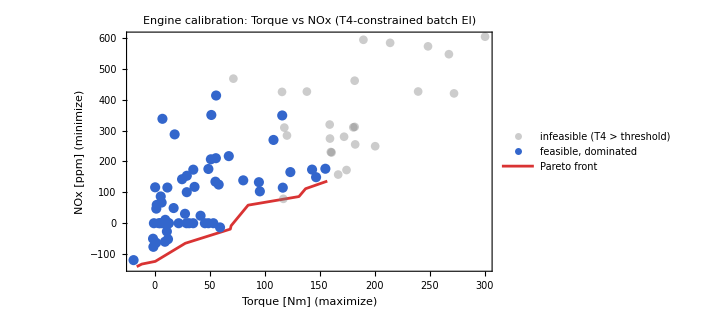

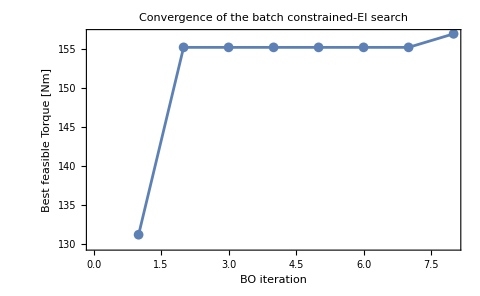

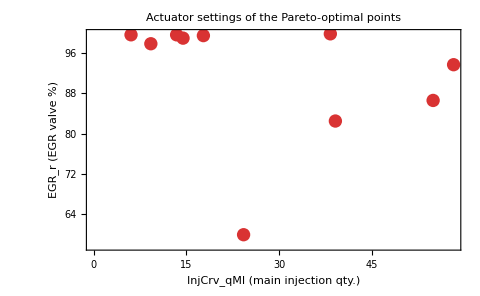

Done. 92 operating points evaluated in total (60 warm-start + 32 proposed by batch constrained-EI).

```mathematica
If[Length[finalFeasIdx] > 0,

 infeasIdx = Complement[Range[Length[Xtrain]], finalFeasIdx];
 dominatedFeasIdx = Complement[finalFeasIdx, paretoGlobalIdx];

 paretoPlot = ListPlot[
   {
    Transpose[{yTorque[[infeasIdx]], yNOx[[infeasIdx]]}],
    Transpose[{yTorque[[dominatedFeasIdx]], yNOx[[dominatedFeasIdx]]}],
    SortBy[Transpose[{yTorque[[paretoGlobalIdx]], yNOx[[paretoGlobalIdx]]}], First]
   },
   PlotStyle -> {
     Directive[Gray, Opacity[0.4], PointSize[0.012]],
     Directive[RGBColor[0.2, 0.4, 0.8], PointSize[0.014]],
     Directive[RGBColor[0.85, 0.2, 0.2], PointSize[0.02]]
   },
   Joined -> {False, False, True},
   PlotLegends -> {"infeasible (T4 > threshold)", "feasible, dominated", "Pareto front"},
   Frame -> True,
   FrameLabel -> {"Torque [Nm]  (maximize)", "NOx [ppm]  (minimize)"},
   PlotLabel -> "Engine calibration: Torque vs NOx (T4-constrained batch EI)",
   ImageSize -> 520
 ];

 convergencePlot = ListLinePlot[
   Select[{#[[1]], #[[2]]} & /@ iterationLog, NumericQ[#[[2]]] &],
   PlotMarkers -> {Automatic, 10},
   Frame -> True,
   FrameLabel -> {"BO iteration", "Best feasible Torque [Nm]"},
   PlotLabel -> "Convergence of the batch constrained-EI search",
   ImageSize -> 480
 ];

 designPlot = ListPlot[
   Transpose[{Xtrain[[paretoGlobalIdx, 3]], Xtrain[[paretoGlobalIdx, 2]]}],
   PlotStyle -> Directive[RGBColor[0.85, 0.2, 0.2], PointSize[0.02]],
   Frame -> True,
   FrameLabel -> {"InjCrv_qMI (main injection qty.)", "EGR_r (EGR valve %)"},
   PlotLabel -> "Actuator settings of the Pareto-optimal points",
   ImageSize -> 480
 ];

 Print[paretoPlot];
 Print[convergencePlot];
 Print[designPlot];
];

Print["\nDone. ", Length[Xtrain], " operating points evaluated in total (",
  nInitTrain, " warm-start + ", Length[Xtrain] - nInitTrain, " proposed by batch constrained-EI)."];
```